```mathematica
phi[x_]:=Exp[-x^2/2]/Sqrt[2*Pi]
```

```mathematica
FLD[x_,gamma_,beta_,alpha_]:= Module[{z1,z2},z1=1/alpha*(Sqrt[(x-gamma)/beta]+Sqrt[beta/(x-gamma)]);z2=1/alpha*(Sqrt[(x-gamma)/beta]-Sqrt[beta/(x-gamma)]);z1/(2*(x-gamma))*phi[z2]]
```

```mathematica
FLD[x,gamma,beta,alpha]
```

(ⅇ^(-(-√(beta/(-gamma+x))+√((-gamma+x)/beta))^2/(2 alpha^2)) (√(beta/(-gamma+x))+√((-gamma+x)/beta)))/(2 alpha √(2 π) (-gamma+x))

```mathematica
Assume[alpha>0 && beta>0 && x>gamma,Solve[D[FLD[x,gamma,beta,alpha],x]==0,x]]
```

$Aborted

```mathematica
FLD2[x_,alpha_]:= Module[{z1,z2},z1=1/alpha*(Sqrt[x]+Sqrt[1/x]);z2=1/alpha*(Sqrt[x]-Sqrt[1/x]);z1/(2*x)*phi[z2]]
```

```mathematica
Solve[D[FLD2[x,alpha],x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/3 (1-alpha^2)-(2^(1/3) (-4-7 alpha^2-alpha^4))/(3 (-16+12 alpha^2-21 alpha^4-2 alpha^6+3 √3 √(-64 alpha^2-64 alpha^4-92 alpha^6-9 alpha^8))^(1/3))+((-16+12 alpha^2-21 alpha^4-2 alpha^6+3 √3 √(-64 alpha^2-64 alpha^4-92 alpha^6-9 alpha^8))^(1/3))/(3 2^(1/3))},{x→1/3 (1-alpha^2)+((1+ⅈ √3) (-4-7 alpha^2-alpha^4))/(3 2^(2/3) (-16+12 alpha^2-21 alpha^4-2 alpha^6+3 √3 √(-64 alpha^2-64 alpha^4-92 alpha^6-9 alpha^8))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (-16+12 alpha^2-21 alpha^4-2 alpha^6+3 √3 √(-64 alpha^2-64 alpha^4-92 alpha^6-9 alpha^8))^(1/3)},{x→1/3 (1-alpha^2)+((1-ⅈ √3) (-4-7 alpha^2-alpha^4))/(3 2^(2/3) (-16+12 alpha^2-21 alpha^4-2 alpha^6+3 √3 √(-64 alpha^2-64 alpha^4-92 alpha^6-9 alpha^8))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (-16+12 alpha^2-21 alpha^4-2 alpha^6+3 √3 √(-64 alpha^2-64 alpha^4-92 alpha^6-9 alpha^8))^(1/3)},{x→1/3 (-1-alpha^2)-(2^(1/3) (-4+7 alpha^2-alpha^4))/(3 (16+12 alpha^2+21 alpha^4-2 alpha^6+3 √3 √(64 alpha^2-64 alpha^4+92 alpha^6-9 alpha^8))^(1/3))+((16+12 alpha^2+21 alpha^4-2 alpha^6+3 √3 √(64 alpha^2-64 alpha^4+92 alpha^6-9 alpha^8))^(1/3))/(3 2^(1/3))},{x→1/3 (-1-alpha^2)+((1+ⅈ √3) (-4+7 alpha^2-alpha^4))/(3 2^(2/3) (16+12 alpha^2+21 alpha^4-2 alpha^6+3 √3 √(64 alpha^2-64 alpha^4+92 alpha^6-9 alpha^8))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (16+12 alpha^2+21 alpha^4-2 alpha^6+3 √3 √(64 alpha^2-64 alpha^4+92 alpha^6-9 alpha^8))^(1/3)},{x→1/3 (-1-alpha^2)+((1-ⅈ √3) (-4+7 alpha^2-alpha^4))/(3 2^(2/3) (16+12 alpha^2+21 alpha^4-2 alpha^6+3 √3 √(64 alpha^2-64 alpha^4+92 alpha^6-9 alpha^8))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (16+12 alpha^2+21 alpha^4-2 alpha^6+3 √3 √(64 alpha^2-64 alpha^4+92 alpha^6-9 alpha^8))^(1/3)}}

```mathematica
Assuming[a1>0,FullSimplify[ComplexExpand[a4-a3/(3 (a2+ⅈ* a1)^(1/3))+(a2+ⅈ* a1)^(1/3)/(3 2^(1/3))]]]
```

a4+(ⅇ^(-1/3 ⅈ Arg[ⅈ a1+a2]) (-2 a3+2^(2/3) (a1^2+a2^2)^(1/3) ⅇ^(2/3 ⅈ Arg[ⅈ a1+a2])))/(6 (a1^2+a2^2)^(1/6))

```mathematica
FullSimplify[D[FLD2[x,alpha],x]]
```

(ⅇ^(-(√(1/x)-√x)^2/(2 alpha^2)) (alpha^2 (-3 (1/x)^(5/2)-1/x^(3/2))-((√(1/x)+√x) (-1+x^2))/x^3))/(4 alpha^3 √(2 π))

```mathematica
N[ReplaceAll[Solve[(ⅇ^(-(√(1/x)-√x)^2/(2 alpha^2)) (alpha^2 (-3 (1/x)^(5/2)-1/x^(3/2))-((√(1/x)+√x) (-1+x^2))/x^3))/(4 alpha^3 √(2 π))==0,x],alpha->4
],70]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2.741348349015881240368964182201132807153935834971993398597795423646786+0. ⅈ},{x→-17.76188580759776474682251084826864250821422137154923556596809443364148+0. ⅈ},{x→0.02053745858188350645354666606750970106028553657724216737029900999469482+0. ⅈ},{x→0.02111513099944644801870221975449042410639318358562783752751532055689035+0. ⅈ},{x→-13.51757134618146430293146270648762435541637203708709942275420810749492+0. ⅈ},{x→-3.503543784817982145087239513266866068690021146498528414773307213061973+0. ⅈ}}

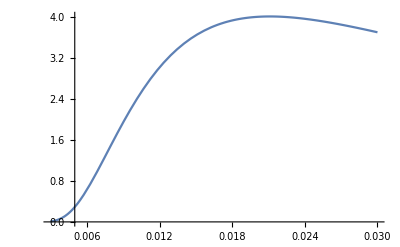

```mathematica
Plot[FLD2[x,4],{x,0.003,0.03}]
```

```mathematica
FullSimplify[ComplexExpand[Solve[D[FLD2[x,alpha],x]==0,x]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

$Aborted

```mathematica
Simplify[Assuming[a1 is Reals && a2 >0,ComplexExpand[a4+a3/(3 (a1+ⅈ*a2)^(1/3))+1/3 (a1+ⅈ*a2)^(1/3)]]]
```

(3 (a1^2+a2^2)^(1/6) a4+((a1^2+a2^2)^(1/3)+a3) Cos[1/3 Arg[a1+ⅈ a2]]+ⅈ ((a1^2+a2^2)^(1/3)-a3) Sin[1/3 Arg[a1+ⅈ a2]])/(3 (a1^2+a2^2)^(1/6))

```mathematica
CForm[Simplify[Take[Solve[D[FLD2[x,alpha],x]==0,x],{1,1}]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

List(List(Rule(x,(2 - 2*Power(alpha,2) + (2*(4 + 7*Power(alpha,2) + Power(alpha,4)))/
         Power(-8 + 6*Power(alpha,2) - (21*Power(alpha,4))/2. - Power(alpha,6) + 
           (3*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))))/2.,0.3333333333333333) + 
        Power(2,0.6666666666666666)*Power(-16 + 12*Power(alpha,2) - 21*Power(alpha,4) - 2*Power(alpha,6) + 
           3*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))),0.3333333333333333))/6.)))

```mathematica
CForm[Simplify[Take[Solve[D[FLD2[x,alpha],x]==0,x],{2,2}]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

List(List(Rule(x,(4 - 4*Power(alpha,2) - (Complex(0,2)*(Complex(0,-1) + Sqrt(3))*(4 + 7*Power(alpha,2) + Power(alpha,4)))/
         Power(-8 + 6*Power(alpha,2) - (21*Power(alpha,4))/2. - Power(alpha,6) + 
           (3*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))))/2.,0.3333333333333333) + 
        Complex(0,1)*Power(2,0.6666666666666666)*(Complex(0,1) + Sqrt(3))*
         Power(-16 + 12*Power(alpha,2) - 21*Power(alpha,4) - 2*Power(alpha,6) + 
           3*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))),0.3333333333333333))/12.)))

```mathematica
CForm[Simplify[Real[Expand[Take[Solve[D[FLD2[x,alpha],x]==0,x],{3,3}]]]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Real(List(List(Rule(x,(-8*Power(2,0.3333333333333333) + Complex(0,8)*Power(2,0.3333333333333333)*Sqrt(3) + 
         Complex(0,2)*Power(2,0.3333333333333333)*(Complex(0,1) + Sqrt(3))*Power(alpha,4) + 
         4*Power(-16 + 12*Power(alpha,2) - 21*Power(alpha,4) - 2*Power(alpha,6) + 
            3*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))),0.3333333333333333) - 
         Power(-32 + 24*Power(alpha,2) - 42*Power(alpha,4) - 4*Power(alpha,6) + 
           6*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))),0.6666666666666666) - 
         Complex(0,1)*Sqrt(3)*Power(-32 + 24*Power(alpha,2) - 42*Power(alpha,4) - 4*Power(alpha,6) + 
            6*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))),0.6666666666666666) + 
         Complex(0,2)*Power(alpha,2)*(Complex(0,7)*Power(2,0.3333333333333333) + 7*Power(2,0.3333333333333333)*Sqrt(3) + 
            Complex(0,2)*Power(-16 + 12*Power(alpha,2) - 21*Power(alpha,4) - 2*Power(alpha,6) + 
               3*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))),0.3333333333333333)))/
       (12.*Power(-16 + 12*Power(alpha,2) - 21*Power(alpha,4) - 2*Power(alpha,6) + 
           3*Sqrt(3)*Sqrt(-(Power(alpha,2)*(64 + 64*Power(alpha,2) + 92*Power(alpha,4) + 9*Power(alpha,6)))),0.3333333333333333))))))

```mathematica
CForm[FullSimplify[Take[Solve[D[FLD2[x,alpha],x]==0,x],{4,4}]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

List(List(Rule(x,(-1 - Power(alpha,2))/3. + (4 - 7*Power(alpha,2) + Power(alpha,4))/
       (3.*Power(8 + 6*Power(alpha,2) + (21*Power(alpha,4))/2. - Power(alpha,6) + 
           (3*Sqrt(3)*Sqrt(64*Power(alpha,2) - 64*Power(alpha,4) + 92*Power(alpha,6) - 9*Power(alpha,8)))/2.,0.3333333333333333)) + 
      Power(8 + 6*Power(alpha,2) + (21*Power(alpha,4))/2. - Power(alpha,6) + 
         (3*Sqrt(3)*Sqrt(64*Power(alpha,2) - 64*Power(alpha,4) + 92*Power(alpha,6) - 9*Power(alpha,8)))/2.,0.3333333333333333)/3.)))

```mathematica
CForm[Simplify[Take[Solve[D[FLD2[x,alpha],x]==0,x],{5,5}]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

List(List(Rule(x,(-1 - Power(alpha,2))/3. + Complex(0,0.16666666666666666)*(Complex(0,1) + Sqrt(3))*
       Power(8 + 6*Power(alpha,2) + (21*Power(alpha,4))/2. - Power(alpha,6) + 
         (3*Sqrt(3)*Sqrt(64*Power(alpha,2) - 64*Power(alpha,4) + 92*Power(alpha,6) - 9*Power(alpha,8)))/2.,0.3333333333333333) - 
      (Complex(0,0.3333333333333333)*(Complex(0,-1) + Sqrt(3))*(4 - 7*Power(alpha,2) + Power(alpha,4)))/
       (Power(2,0.6666666666666666)*Power(16 + 12*Power(alpha,2) + 21*Power(alpha,4) - 2*Power(alpha,6) + 
           3*Sqrt(3)*Sqrt(64*Power(alpha,2) - 64*Power(alpha,4) + 92*Power(alpha,6) - 9*Power(alpha,8)),0.3333333333333333)))))

```mathematica
CForm[FullSimplify[Take[Solve[D[FLD2[x,alpha],x]==0,x],{6,6}]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

List(List(Rule(x,(-1 - Power(alpha,2))/3. + (Power(-1,0.6666666666666666)*(4 - 7*Power(alpha,2) + Power(alpha,4)))/
       (3.*Power(8 + 6*Power(alpha,2) + (21*Power(alpha,4))/2. - Power(alpha,6) + 
           (3*Sqrt(3)*Sqrt(64*Power(alpha,2) - 64*Power(alpha,4) + 92*Power(alpha,6) - 9*Power(alpha,8)))/2.,0.3333333333333333)) - 
      (Power(-0.5,0.3333333333333333)*Power(16 + 12*Power(alpha,2) + 21*Power(alpha,4) - 2*Power(alpha,6) + 
           3*Sqrt(3)*Sqrt(64*Power(alpha,2) - 64*Power(alpha,4) + 92*Power(alpha,6) - 9*Power(alpha,8)),0.3333333333333333))/3.)))